# Running through the Seasons

## Predicting Runs Based on Environmental Data

Stephen Schroeder

## Introduction

"Whether the weather is fine, or whether the weather is not; whether the weather is cold, or whether the weather is hot; we'll weather the weather, whatever the weather, whether we like it or not!"
-Unknown

After a few years of running, I have ideas about things that might affect my running, but previously I had not done any rigorous analysis. I know I run less in the middle of the winter, and I run more during the summer, but how much more exactly? Wolfram Language allows for all of my abstract thoughts to be crystallised with my runs tracked using RunKeeper! Normally, I don’t go out with a plan for how long I will run, and I turn back based on how I am feeling that day as long as my run is at least 2km. Because of this, one of the main questions that I have about my running data is how my running is affected by temperature, and if I can predict how long I will run, given a temperature outside.

## Running Data Preparation

### Importing Running Data

Previously, I used ServiceConnect to fetch my running data, but unfortunately ServiceConnect does not fetch GPS data. And I will need location data to be able to know what the outside temperature was at the time of my run.
In order to do that, I manually exported my data from my RunKeeper account as explained here, and saved the data to my NotebookDirectory[] with all the GPS files in their own folder.
Now, to get started, all the data needs to be imported. I imported the data in a similar fashion to this fantastic Wolfram Blog post, where the running data is parsed using the smart SemanticImport on the .csv file from RunKeeper. Feel free to follow along with your own data, or, if you’d rather just see the demonstration, just evaluate (⇧+⌤) the SetDirectory and  <<expressions.mx functions in the next cell and read the rest.

```mathematica
SetDirectory[NotebookDirectory[]];
Import["https://github.com/StephenSchroeder/WolframSummer2019/blob/master/Homework/Drafts/expressions.mx?raw=true"]
```

```mathematica
runningData = SemanticImport[
	"cardioActivities.csv",
	{"String","Date","String","String",Restricted["Quantity","Kilometers"],
	"String","String",Restricted["Quantity",("Kilometers")/("Hours")],Restricted["Quantity","LargeCalories"],
	Restricted["Quantity","Meters"],"String","String","String","String"
	}
];
```

To import the GPS data, I put all the .gpx files in their own folder called GPS. If you’re following along you will need to do this as well. I only need the first GPS coordinate from each run, so I used First to individually select that.

```mathematica
importGPSData[] := importGPSData[FileNames["*.gpx", "GPS"]]
importGPSData[files_List] := Association@ Map[importGPSData, files]
importGPSData[file_String] :=FileNameTake[file] ->  First @ Cases[
Import[file, "XML"], XMLElement["trkpt",{"lat"->lat_,"lon"->lon_},{_,XMLElement["time",{},{time_}]}] :> {time, lat, lon}, 
Infinity
];

rawGPSData = importGPSData[];
```

Now, so I can best use the GPS data, I will make sure that it is explicitly made up of lists of GeoPosition.

```mathematica
GPSData = Map[
GeoPosition@{ToExpression[#[[2]]], ToExpression[#[[3]]]} &, 
rawGPSData
];
```

Lastly, the data needs to be added alongside the rest of the running data imported earlier into our now nice looking dataset!

```mathematica
runningDataWithGPS = Map[
Append[#, "GeoCoord" -> GPSData[#["GPX File"]]]&,
runningData
];
```

### Getting Date-time and Location Specific Temperatures

In order to discover how temperature affects how long I run, I still need to get the temperature data. Thankfully, Location and Time-Specific data is available using the Wolfram Language’s integrated knowledge. I’ll also clean up some missing GPS data to avoid errors.

```mathematica
coords = DeleteCases[Values@Normal@runningDataWithGPS[[All, {"GeoCoord", "Date"}]], {_Missing, _}];
tempData = AirTemperatureData[coords,UnitSystem->"Metric"];
```

Finally, all that needs to be done is to add this data to the dataset!

```mathematica
tempDataAssoc = AssociationThread[coords -> tempData];
```

```mathematica
runningDataWithGPSandTemp = Map[
Append[#, "Temperature" -> tempDataAssoc[{#["GeoCoord"],#["Date"]}]]&,
runningDataWithGPS
];
```

All the data is ready, so it’s time to visualise and understand how temperature really effects my running.

## Data Visualisation and Evaluation

Now it' s possible to do tons of analysis of my running data! First, we can see the starting locations of my runs over the past  2 years. Lots of running in icy Canada.

```mathematica
geodata = Flatten[
			Cases[coords,GeoPosition[place__]:>{place},Infinity]
				,1];
```

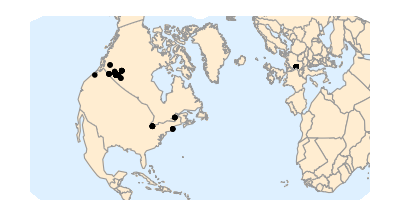

```mathematica
GeoGraphics[GeoMarker[geodata],GeoBackground->"CountryBorders"]
```

The next plot provides real evidence that those cold winters do cause my running distance to go down! It seems like there must be some correlation there.

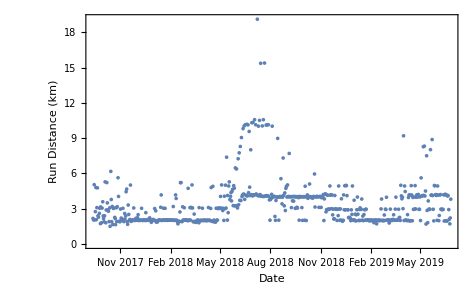

```mathematica
DateListPlot[Query[All,{"Date","Distance (km)"}]@runningDataWithGPSandTemp,Axes->True,FrameLabel->{"Date","Run Distance (km)"},Joined->False,PlotRange->All]
```

### Distance as a function of temperature

This is what everything has been building to! To visualise the data, all that needs to be done is pair the temperature at the time and location of my run with the distance of my run:

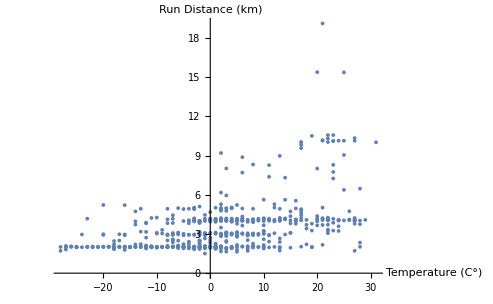

```mathematica
ListPlot[Query[All,{"Temperature","Distance (km)"}]@runningDataWithGPSandTemp,AxesLabel->{"Temperature (C°)","Run Distance (km)"},PlotRange->All]
```

This ListPlot shows how my run distance increases with temperature, just like I predicted. Looking at this data, there doesn’t seem to be a strong correlation between the temperature and how far I run, but it’ll still be possible to make a predictive function!

## How Far Will I Run in the Cold or the Heat?

### Making a Predictive Function

Now that all the data is together, we can train an algorithm on my running data, and answer the original question. We just have to feed in the data to a prediction algorithm as a nice, clean list of rules.

```mathematica
tempdistassoc=Cases[runningDataWithGPSandTemp//Normal//Values,{__,Quantity[distance_,"Kilometers"],__,Quantity[temperature_,"DegreesCelsius"]}:>{temperature->distance},Infinity];
```

```mathematica
distpredict=Predict[Flatten[tempdistassoc],Method->"NearestNeighbors"]
```

PredictorFunction[…]

Using the predictor, it’s easy to make an interactive tool to predict how far I will run based on a temperature. Try it out! (If the interactive cell looks funny, try ⇧+⌤ on the In cell just before it)

```mathematica
Manipulate[StringJoin["Predicted Running Distance: ",ToString[distpredict[x]]," kms"],{{x,15,"Temperature (°C)"},-30,30,1,Appearance->"Open"},AppearanceElements->All]
```

This is the plot of predicted run distance against temperature, with the previous points overlaid. The plot shows how my runs are generally quite short when the temperature is below 0°C, and quickly increase in average distance as the temperature increases. It also shows how above ~20°C my runs don’t keep linearly increasing in distance due to the heat.  Although this may not be surprising, the model decent job of showing the trends in my running data, and it shows how computational thinking can be used to track personal fitness and learn about yourself.

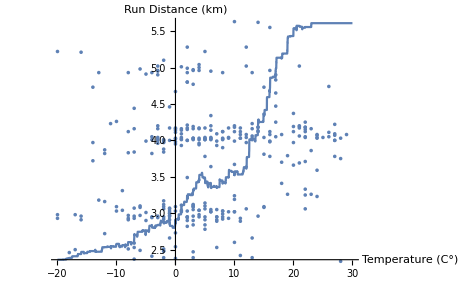

```mathematica
Show[Plot[distpredict[x],{x,-20,30},Exclusions->None],ListPlot[Cases[tempdistassoc,{t_->d_}:>{t,d},Infinity]],AxesLabel->{"Temperature (C°)","Run Distance (km)"}]
```

If I want to challenge myself, I can even try to beat the predictive algorithm, and set out to run at least as long as the prediction based on the forecast. I am looking forward to seeing how the predictive algorithm changes based on how I run in the future!